```mathematica
data = {{100000,0.0708694},{200000,0.145892},{300000,0.220806},{400000,0.295793},{500000,0.372564},{600000,0.42589},{700000,0.504546},{800000,0.5871},{900000,0.659024},{1000000,0.73479}}
```

{{100000,0.0708694},{200000,0.145892},{300000,0.220806},{400000,0.295793},{500000,0.372564},{600000,0.42589},{700000,0.504546},{800000,0.5871},{900000,0.659024},{1000000,0.73479}}

```mathematica
Fit[data,{1,x*Log[x]},x]
```

0.0205561+5.18393×10^-8 x Log[x]

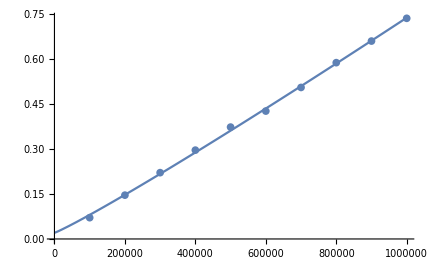

```mathematica
Show[{Plot[%22,{x,0,1000000}], ListPlot[data]}]
```

```mathematica
NonlinearModelFit[data,{1,x*Log[x]},{goo}, x]
```

NonlinearModelFit::lss: {} should be a non-empty list of search specifications, each consisting of a variable and possibly starting values.

NonlinearModelFit[{{100000,0.0708694},{200000,0.145892},{300000,0.220806},{400000,0.295793},{500000,0.372564},{600000,0.42589},{700000,0.504546},{800000,0.5871},{900000,0.659024},{1000000,0.73479}},{1,x Log[x]},{},x]

```mathematica
nlm = NonlinearModelFit[data,{a*x*Log[x]+b},{a,b},x]
```

FittedModel[0.0205561+5.18393×10^-8 x Log[x]]

```mathematica
nlm // Normal
```

0.0205561+5.18393×10^-8 x Log[x]

```mathematica
FindFit[data,{a*x*Log[x]+b},{a,b},x]
```

{a→5.18393×10^-8,b→0.0205561}

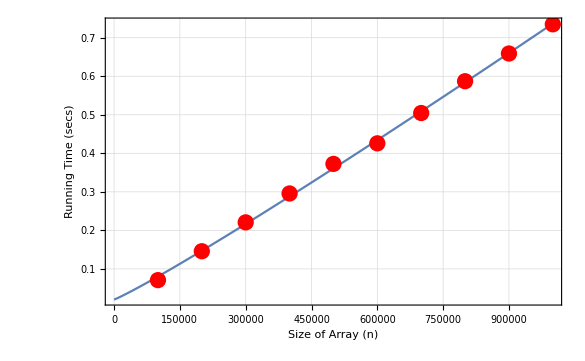

```mathematica
Show[Plot[nlm[x], {x, 0,1000000},PlotRange->All,GridLines->Automatic,Frame->True,FrameLabel->{"Size of Array (n)", "Running Time (secs)"}],ListPlot[data, PlotStyle->Directive[Red,PointSize[0.02]]]]
```

```mathematica
nlm["RSquared"]
```

0.999799

```mathematica
nlm["AdjustedRSquared"]
```

0.999749

```mathematica
Log[2.50565]
```

0.918548